```mathematica
ME314 Final Project;
FeiyuChen;
This is the __main__ file of my project;
```

```mathematica
(*Quit[]*)
(*Open and run all other Mathematica scripts*)
myOpenFile[filename_]:=Module[{nb1},nb1=NotebookOpen[NotebookDirectory[]<>"/"<>filename];
     SelectionMove[nb1,All,Notebook];
     SelectionEvaluate[nb1]
]
myOpenFile["funcs_math.nb"];
myOpenFile["funcs_assist.nb"];
myOpenFile["funcs_main.nb"];
```

```mathematica
(*Put your code here to create links system*)
CreateObjects:=Module[{},

(* ------ Output of createLink ------
The "link" variable returned by createLink has 5 elements;
{T,pFront,pBack,TFront,TBack};

If you want to use them for adding constraint or extending other links,You can access them by these indices:
IdxT=1;IdxPFront=2;IdxPBack=3;IdxTFront=4;IdxTBack=5;

Such as:
link1=createLink3DOFpp[p0,p1]
link1[[IdxTFront]]
*)

(* Example 1: Polygon with NumOfEdges *)
nthGroup=1;(* Objects in side one group won't collide with each other *)
initRandVelocity=1.0;(* max of the random initial velocity*)

p0={-1,0};
p1={-0.5,0.2};
l=CalcDistpp[p0,p1];

NumOfEdges=5;(* create a pentagon *)
linki=createLink3DOFpp[p0,p1];
For[i=1,i≤NumOfEdges,i=i+1,
linki=createLink0DOFgθl[linki[[IdxTFront]],2*Pi/NumOfEdges,l]
];

(* Example 2: 2-links *)
(*create a vertex first, then append link to it.*)
nthGroup=2;
initRandVelocity=1.0;

gFix=Trans4[0,1];
createVertex[gFix];
linki=createLink1DOFgθl[gFix,0,1.2];
linki=createLink1DOFgθl[linki[[IdxTFront]],-3*Pi/4,1.5];

(* Example 3: 1-link pendulum with its origin constrained at a fixed height*)
nthGroup=3;
initRandVelocity=0;

p0={1.5,1.8};
p1={2.0,1.6};

linki=createLink3DOFpp[p0,p1];
addConstraint[linki[[IdxPBack]][[2]]==0];

(* Example 4: A square wall with 4 edges *);
nthGroup=10;
pWalls={{-2,+2.2},{+2.2,+1},{+2,-2.2},{-2.2,-2}};
AppendTo[pWalls,pWalls[[1]]];
For[i=1,i≤4,i++,
createLink0DOFpp[pWalls[[i]],pWalls[[i+1]]]
];

(* Example 5: A wall in the middle *)
createLink0DOFpp[{1,-1.2},{1.5,-0.6}];

];
```

```mathematica
(* Set up all things *)
mainResetVars;
CreateObjects;
RemoveDuplicateVertexs;

externalForces=ConstantArray[0,nVars];

Print["\nStart Solving ..."];
mainSolveELeqs;
Print["Finish Solving ..."];

ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];

Print["\nStart setting impact ..."];
SetUpImpacts[];
Print["Finish setting impact ..."];
```

Start Solving ...

Finish Solving ...

Start setting impact ...

Finish setting impact ...

Computing simulation: 2.12359 / 10 ...

Computing simulation: 4.05388 / 10 ...

Computing simulation: 6.2298 / 10 ...

Computing simulation: 8.19909 / 10 ...

Computing simulation is completed.

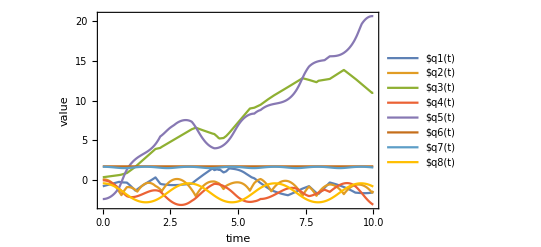

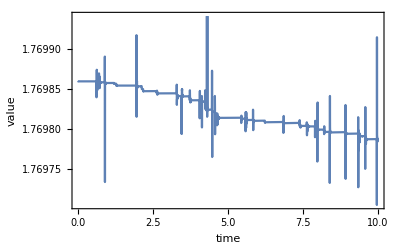

```mathematica
(* Set up params for NDSolve *)
timeend=10;(* total simulation time *)
MAXIMPACTTIMES=1000;
impactDetectionError=0.05;
intergrationMaxStepSize=0.005;
ifprint=False;

(* NDsolve and Play simulation *)
{end,data,bounces}=mainNDSolveSimulation[qsInit,dqsInit];

(* Plot *)
plotVariablesValues
plotHamValues
plotAnimation
```